numberOfBasisCell (-1+(1+2 numberOfSurroundingCells)^2)

1/6 numberOfBasisCell (2-3 numberOfBasisCell+numberOfBasisCell^2)+2 (-1+numberOfBasisCell) numberOfBasisCell^2 numberOfSurroundingCells (1+numberOfSurroundingCells)+2 numberOfBasisCell^2 (numberOfSurroundingCells+numberOfSurroundingCells^2) (-1+4 numberOfBasisCell numberOfSurroundingCells+4 numberOfBasisCell numberOfSurroundingCells^2)

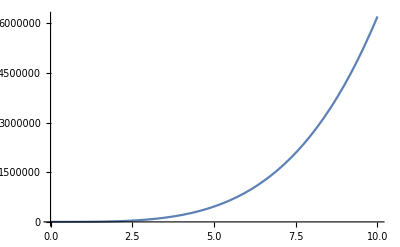

```mathematica
numberOfOtherSpace = numberOfBasisCell*((2*numberOfSurroundingCells+1)^2-1)

numberOfTriangles = Sum[Sum[Sum[1,{k, j+1, numberOfBasisCell-1}],{j, i+1,  numberOfBasisCell-1}],{i, 0,  numberOfBasisCell-1}]+ Sum[Sum[Sum[1,{k, 0, numberOfOtherSpace-1}],{j, i+1,  numberOfBasisCell-1}],{i, 0,  numberOfBasisCell-1}]+Sum[Sum[Sum[1,{k, j+1, numberOfOtherSpace-1}],{j, 0,  numberOfOtherSpace-1}],{i, 0,  numberOfBasisCell-1}]

Plot[numberOfTriangles/.{numberOfBasisCell->4}, {numberOfSurroundingCells,0,10}]
```

(1/6 numberOfBasisCell (2-3 numberOfBasisCell+numberOfBasisCell^2)+2 (-1+numberOfBasisCell) numberOfBasisCell^2 numberOfSurroundingCells (1+numberOfSurroundingCells)+2 numberOfBasisCell^2 (numberOfSurroundingCells+numberOfSurroundingCells^2) (-1+4 numberOfBasisCell numberOfSurroundingCells+4 numberOfBasisCell numberOfSurroundingCells^2)) timePerTriangle

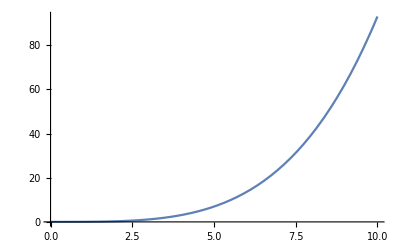

```mathematica
timeNeeded = timePerTriangle*numberOfTriangles

Plot[timeNeeded/.{timePerTriangle->15*10^-6, numberOfBasisCell->4}, {numberOfSurroundingCells,0,10}]
```

Other stuff here

```mathematica
numberOfTriangles/.{numberOfSurroundingCells->4, numberOfBasisCell->4}
Simplify[numberOfTriangles/.{numberOfSurroundingCells->x, numberOfBasisCell->y}]
```

206084

1/6 y (2-3 y+12 x (1+x) (-1+y) y+y^2+12 x (1+x) y (-1+4 x y+4 x^2 y))